# Regulating Expectation Values in Time Dependent QFTs

## Definitions

```mathematica
win=√(k^2+m^2(A-B));
wout=√(k^2+m^2(A+B));
wplus=1/2(win+wout);
wminus=1/2(-win+wout);
```

```mathematica
A=1/2;
B=-1/2;
m=1;
m2[t_]:=A+B Tanh[ρ t];
```

ρ = 1/δt will be our preferred variable here. η is the conformal time.

```mathematica
hyper=Hypergeometric2F1[1+ⅈ wminus/ρ,ⅈ wminus/ρ,1-ⅈ win/ρ,1/2(1+Tanh[ρ η])];
```

## d=7 case

We want to regulate the following expectation value:
<ϕ^2(η)> = ∫ dk k^(d-2)/ω_in|_2 F_1(1+ⅈ (ω_-)/ρ,ⅈ (ω_-)/ρ;1-ⅈ ω_in/ρ;1/2(1+Tanh[ρ η]))|^2

We start by finding the divergent terms of the constant mass case

```mathematica
Clear[m];
Series[Integrate[k^(7-2)/(√(k^2+m^2)),{k,0,kmax}],{kmax, ∞,3}]
```

ConditionalExpression[kmax^5/5-(m^2 kmax^3)/6+(3 m^4 kmax)/8-8/15 (m^4 √(m^2))+(5 m^6)/(16 kmax)-(35 m^8)/(384 kmax^3)+O[1/kmax]^4,!(1/kmax|m)∈Reals||m/kmax≠0||m Im[kmax]==0]

```mathematica
int=(k^(7-2)/win Abs[hyper]^2-(k^4-m2[η]/2 k^2+3/8 m2[η]^2))//Rationalize;
```

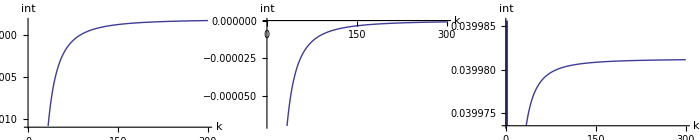

```mathematica
GraphicsRow[Table[Plot[int/.ρ:>1/.m:>1,{k,0,300},AxesLabel->{"k","int"},WorkingPrecision->50],{η,-1,1,1}],ImageSize->700]
```

Oops! The integrand goes to a constant, so if we integrate to ∞ it will diverge! There is a counterterm missing. Let’s find it!

## Finding the extra counterterm

To do this, we will fix the momentum to some large value k0 and see what happens as a function of time η.

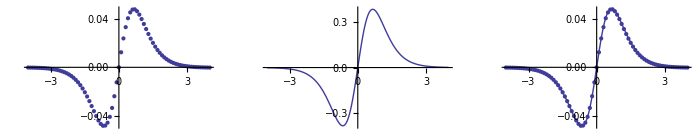

```mathematica
k0=200;
table=Table[{η,(k^(7-2)/win Abs[hyper]^2-(k^4-m2[η]/2 k^2+3/8 m2[η]^2))/.ρ:>1/.m:>1/.k:>k0},{η,-4,4,0.1}];
GraphicsRow[{ListPlot[%],Plot[ρ^2 Sech[t ρ]^2 Tanh[t ρ]/.t:>η/.ρ:>1,{η,-4,4}],Show[ListPlot[table],Plot[{(-2 B ρ^2 Sech[η ρ]^2 Tanh[η ρ])/8/.ρ:>1},{η,-4,4}]]},ImageSize->700]
```

Wow! But doesn’t that look like some derivative of the mass?

```mathematica
model=a*(ρ^2 Sech[η ρ]^2 Tanh[η ρ])/.ρ:>1;
```

```mathematica
ρ=1;fit=FindFit[table,{model},{a},η]
```

{a→0.124354}

After repeating the procedure for differnet k0 (and thinking that this coefficient should come from a reasonable expansion), one realizes that 0.12345 ~ 0.125 =1/8

So the finite regulated function is

```mathematica
Clear[ρ];int=(k^(7-2)/win Abs[hyper]^2-(k^4-m2[η]/2 k^2+3/8 m2[η]^2+1/8( ρ^2 Sech[η ρ]^2 Tanh[η ρ])))
```

-k^4+1/(√(k^2+m^2))k^5 Abs[Hypergeometric2F1[1+(ⅈ (√(k^2)-√(1+k^2)))/(2 ρ),(ⅈ (√(k^2)-√(1+k^2)))/(2 ρ),1-(ⅈ √(1+k^2))/ρ,1/2 (1+Tanh[η ρ])]]^2+1/2 k^2 (1/2-1/2 Tanh[η ρ])-3/8 (1/2-1/2 Tanh[η ρ])^2-1/8 ρ^2 Sech[η ρ]^2 Tanh[η ρ]

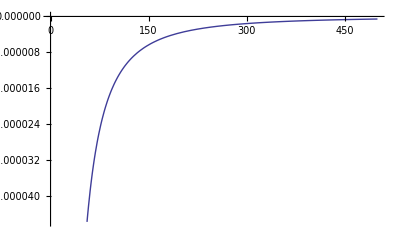
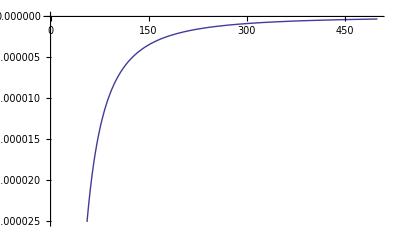
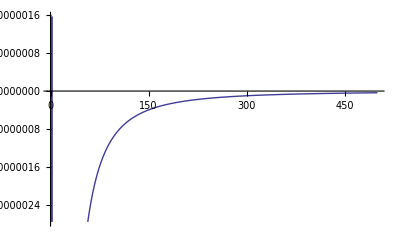

```mathematica
Table[Plot[int/.ρ:>1/.m:>1,{k,0,500},WorkingPrecision->30],{η,-1/ρ,1/ρ,1/ρ}]
```

And in fact it goes to zero as k->∞.

## Extras

So now we can compute the regulated expectation value for any value of ρ! In this case, say ρ = 10 :

```mathematica
ρ=10;m=1;rho10=Table[{ρ η,(NIntegrate[int,{k,0,200}])},{η,-3/ρ,3/ρ,0.10/ρ}];
ListLinePlot[rho10,PlotStyle->Thick,Frame->True,FrameLabel->{"ρ η", "<ϕ^2>_ren(η)"}]
```

This expectation value is UV-finite and it scales as ρ^(d-4)=ρ^3 in this case, exactly the same scaling that one would find in an holographic quench of a dimension Δ=d-2 operator. Moreover, we were able to find the analytic expression for the expectation value in the limit of ρ->∞ (dashed red in the second figure). But that’s for the next Mathematica School!

```mathematica
-Graphics--Graphics-
```